```mathematica
data = Import["C:\\Users\\Owner\\Desktop\\ACM Spring 23 Research Coding Challenge\\6 class csv.csv"]
```

{{Temperature (K),Luminosity(L/Lo),Radius(R/Ro),Absolute magnitude(Mv),Star type,Star color,Spectral Class},{3068,0.0024,0.17,16.12,0,Red,M},{3042,0.0005,0.1542,16.6,0,Red,M},{2600,0.0003,0.102,18.7,0,Red,M},{2800,0.0002,0.16,16.65,0,Red,M},{1939,0.000138,0.103,20.06,0,Red,M},{2840,0.00065,0.11,16.98,0,Red,M},{2637,0.00073,0.127,17.22,0,Red,M},{2600,0.0004,0.096,17.4,0,Red,M},{2650,0.00069,0.11,17.45,0,Red,M},{2700,0.00018,0.13,16.05,0,Red,M},{3600,0.0029,0.51,10.69,1,Red,M},{3129,0.0122,0.3761,11.79,1,Red,M},{3134,0.0004,0.196,13.21,1,Red,M},{3628,0.0055,0.393,10.48,1,Red,M},{2650,0.0006,0.14,11.782,1,Red,M},{3340,0.0038,0.24,13.07,1,Red,M},{2799,0.0018,0.16,14.79,1,Red,M},{3692,0.00367,0.47,10.8,1,Red,M},{3192,0.00362,0.1967,13.53,1,Red,M},{3441,0.039,0.351,11.18,1,Red,M},{25000,0.056,0.0084,10.58,2,Blue White,B},{7740,0.00049,0.01234,14.02,2,White,A},{7220,0.00017,0.011,14.23,2,White,F},{8500,0.0005,0.01,14.5,2,White,A},{16500,0.013,0.014,11.89,2,Blue White,B},{12990,0.000085,0.00984,12.23,2,Yellowish White,F},{8570,0.00081,0.0097,14.2,2,Blue white,A},{7700,0.00011,0.0128,14.47,2,Yellowish White,F},{11790,0.00015,0.011,12.59,2,Yellowish White,F},{7230,0.00008,0.013,14.08,2,Pale yellow orange,F},{39000,204000,10.6,-4.7,3,Blue,O},{30000,28840,6.3,-4.2,3,Blue-white,B},{15276,1136,7.2,-1.97,3,Blue-white,B},{9700,74,2.89,0.16,3,Whitish,B},{5800,0.81,0.9,5.05,3,yellow-white,F},{8052,8.7,1.8,2.42,3,Whitish,A},{6757,1.43,1.12,2.41,3,yellow-white,F},{6380,1.35,0.98,2.93,3,yellow-white,F},{5936,1.357,1.106,4.46,3,yellow-white,F},{5587,0.819,0.99,5.03,3,yellow-white,F},{3826,200000,19,-6.93,4,Red,M},{3365,340000,23,-6.2,4,Red,M},{3270,150000,88,-6.02,4,Red,M},{3200,195000,17,-7.22,4,Red,M},{3008,280000,25,-6,4,Red,M},{3600,320000,29,-6.6,4,Red,M},{3575,123000,45,-6.78,4,Red,M},{3574,200000,89,-5.24,4,Red,M},{3625,184000,84,-6.74,4,Red,M},{33750,220000,26,-6.1,4,Blue,B},{3490,270000,1520,-9.4,5,Red,M},{3750,283000,1260,-7.63,5,Red,M},{3834,272000,1183,-9.2,5,Red,M},{3749,550000,1648,-8.05,5,Orange,M},{3650,310000,1324,-7.79,5,Red,M},{3450,263000,1349,-11.75,5,Red,M},{3660,363000,1673,-11.92,5,Red,M},{3450,174000,1284,-11.28,5,Red,M},{3752,209000,955,-11.24,5,Red,M},{3535,195000,1546,-11.36,5,Red,M},{3341,0.0056,0.057,16.23,0,Red,M},{3432,0.00067,0.19,16.94,0,Red,M},{2983,0.00024,0.094,16.09,0,Red,M},{2835,0.00034,0.0918,16.96,0,Red,M},{2935,0.00014,0.116,18.89,0,Red,M},{3295,0.00098,0.132,17.13,0,Red,M},{2945,0.00032,0.093,18.34,0,Red,M},{2817,0.00098,0.0911,16.45,0,Red,M},{2774,0.00036,0.118,17.39,0,Red,M},{2871,0.00072,0.12,19.43,0,Red,M},{3345,0.021,0.273,12.3,1,Red,M},{3607,0.022,0.38,10.12,1,Red,M},{3304,0.0085,0.18,13.2,1,Red,M},{3150,0.0088,0.35,11.94,1,Red,M},{3550,0.004,0.291,10.89,1,Red,M},{3180,0.001,0.35,11.76,1,Red,M},{2890,0.0034,0.24,13.46,1,Red,M},{3342,0.0015,0.307,11.87,1,Red,M},{2621,0.0006,0.098,12.81,1,Red,M},{3158,0.00135,0.161,13.98,1,Red,M},{7100,0.00029,0.012,14.09,2,White-Yellow,F},{10574,0.00014,0.0092,12.02,2,White,F},{8930,0.00056,0.0095,13.78,2,white,A},{17200,0.00098,0.015,12.45,2,Blue White,B},{14100,0.00067,0.0089,12.17,2,Blue White,B},{9675,0.00045,0.0109,13.98,2,Blue White,A},{12010,0.00078,0.0092,12.13,2,Blue White,B},{10980,0.00074,0.0087,11.19,2,Blue White,B},{13720,0.00018,0.00892,12.97,2,white,F},{19860,0.0011,0.0131,11.34,2,Blue,B},{5300,0.59,0.91,5.49,3,yellow-white,F},{4526,0.153,0.865,6.506,3,yellowish,K},{4077,0.085,0.795,6.228,3,yellowish,K},{4980,0.357,1.13,4.78,3,Yellowish,K},{9030,45,2.63,1.45,3,Blue-white,A},{11250,672,6.98,-2.3,3,Blue-white,A},{5112,0.63,0.876,4.68,3,Orange-Red,K},{7720,7.92,1.34,2.44,3,yellow-white,F},{12098,689,7.01,0.02,3,Blue-white,A},{36108,198000,10.2,-4.4,3,Blue,O},{33300,240000,12,-6.5,4,Blue,B},{40000,813000,14,-6.23,4,Blue,O},{23000,127000,36,-5.76,4,Blue,O},{17120,235000,83,-6.89,4,Blue,O},{11096,112000,12,-5.91,4,Blue,O},{14245,231000,42,-6.12,4,Blue,O},{24630,363000,63,-5.83,4,Blue,O},{12893,184000,36,-6.34,4,Blue,O},{24345,142000,57,-6.24,4,Blue,O},{33421,352000,67,-5.79,4,Blue,O},{3459,100000,1289,-10.7,5,Red,M},{3605,126000,1124,-10.81,5,Red,M},{3615,200000,1635,-11.33,5,Red,M},{3399,117000,1486,-10.92,5,Red,M},{3610,132000,1522,-10.86,5,Red,M},{3553,145000,1324,-11.03,5,Red,M},{4015,282000,1534,-11.39,5,Red,K},{3625,74000,876,-10.25,5,Red,M},{6850,229000,1467,-10.07,5,Red,G},{3780,200000,1324,-10.7,5,Red,M},{3323,0.00043,0.0912,17.16,0,Red,M},{3531,0.00093,0.0976,19.94,0,Red,M},{3218,0.00054,0.11,20.02,0,Red,M},{3146,0.00015,0.0932,16.92,0,Red,M},{3511,0.00064,0.109,17.12,0,Red,M},{3225,0.00076,0.121,19.63,0,Red,M},{2935,0.00087,0.0932,16.88,0,Red,M},{2861,0.00019,0.0899,16.71,0,Red,M},{2856,0.000896,0.0782,19.56,0,Red,M},{2731,0.000437,0.0856,18.09,0,Red,M},{3095,0.00019,0.492,10.87,1,Red,M},{3607,0.00023,0.38,10.34,1,Red,M},{3100,0.008,0.31,11.17,1,Red,M},{2989,0.0087,0.34,13.12,1,Red,M},{3542,0.0009,0.62,14.23,1,Red,M},{3243,0.0023,0.73,14.75,1,Red,M},{3091,0.0081,0.24,11.43,1,Red,M},{3598,0.0011,0.56,14.26,1,Red,M},{3324,0.0034,0.34,12.23,1,Red,M},{3541,0.0013,0.256,14.33,1,Red,M},{13420,0.00059,0.00981,13.67,2,Blue White,B},{21020,0.0015,0.0112,11.52,2,Blue,B},{18290,0.0013,0.00934,12.78,2,Blue,B},{14520,0.00082,0.00972,11.92,2,Blue White,B},{11900,0.00067,0.00898,11.38,2,Blue white,B},{8924,0.00028,0.00879,14.87,2,Blue white,A},{12912,0.00071,0.00945,12.83,2,Blue white,B},{14732,0.00011,0.00892,12.89,2,white,F},{7723,0.00014,0.00878,14.81,2,White,A},{12984,0.00088,0.00996,11.23,2,Blue White,B},{29560,188000,6.02,-4.01,3,Blue-white,B},{8945,38,2.487,0.12,3,Blue-White,A},{14060,1092,5.745,-2.04,3,Blue-white,A},{16390,1278,5.68,-3.32,3,Blue-white,B},{25070,14500,5.92,-3.98,3,Blue-white,B},{28700,16790,6.4,-4.09,3,Blue-white,B},{26140,14520,5.49,-3.8,3,Blue-white,B},{20120,4720,6.78,-3.4,3,Blue-white,B},{13023,998,6.21,-1.38,3,Blue-white,A},{37800,202900,6.86,-4.56,3,Blue,O},{25390,223000,57,-5.92,4,Blue,O},{11567,251000,36,-6.245,4,Blue,O},{12675,452000,83,-5.62,4,Blue,O},{5752,245000,97,-6.63,4,Blue,O},{8927,239000,35,-7.34,4,Blue,O},{7282,131000,24,-7.22,4,Blue,O},{19923,152000,73,-5.69,4,Blue,O},{26373,198000,39,-5.83,4,Blue,O},{17383,342900,30,-6.09,4,Blue,O},{9373,424520,24,-5.99,4,Blue,O},{3570,320000,1480,-7.58,5,Red,M},{3500,138000,1420,-8.18,5,Red,M},{4287,630000,1315,-9.2,5,Orange,K},{26000,316000,1679,-9.1,5,Blue,B},{3600,240000,1190,-7.89,5,Red,M},{3614,145000,1553,-7.71,5,Red,M},{18000,200000,1045,-8.3,5,Blue,O},{11000,170000,1779,-9.9,5,Blue-white,B},{12100,120000,708.9,-7.84,5,Blue-white,B},{24490,248490,1134.5,-8.24,5,Blue-white,B},{2831,0.000231,0.0915,16.21,0,Red,M},{2914,0.000631,0.116,18.39,0,Red,M},{3419,0.000245,0.126,17.56,0,Red,M},{3218,0.000452,0.0987,17.34,0,Red,M},{3453,0.000621,0.0773,17.08,0,Red,M},{2889,0.000352,0.0973,16.93,0,Red,M},{2968,0.000461,0.119,17.45,0,Red,M},{3484,0.000551,0.0998,16.67,0,Red,M},{2778,0.000849,0.112,19.45,0,Red,M},{3523,0.000957,0.129,16.35,0,Red,M},{3462,0.0053,0.148,11.47,1,Red,M},{3257,0.0024,0.46,10.73,1,Red,M},{2994,0.0072,0.28,13.45,1,Red,M},{3212,0.0016,0.378,12.854,1,Red,M},{3523,0.0054,0.319,12.43,1,Red,M},{3598,0.0027,0.67,13.667,1,Red,M},{3142,0.00132,0.258,14.12,1,Red,M},{3496,0.00125,0.336,14.94,1,Red,M},{3324,0.0065,0.471,12.78,1,Red,M},{3463,0.0027,0.675,14.776,1,Red,M},{16790,0.0014,0.0121,12.87,2,Blue,B},{15680,0.00122,0.0114,11.92,2,Blue,B},{14982,0.00118,0.0113,12.23,2,Blue,B},{13340,0.00109,0.0116,12.9,2,Blue,B},{18340,0.00134,0.0124,11.22,2,Blue,B},{19920,0.00156,0.0142,11.34,2,Blue,B},{24020,0.00159,0.0127,10.55,2,Blue,B},{23092,0.00132,0.0104,10.18,2,Blue,B},{17920,0.00111,0.0106,11.66,2,Blue,B},{19360,0.00125,0.00998,11.62,2,Blue,B},{22350,12450,6.36,-3.67,3,Blue-white,B},{10012,552,5.856,0.013,3,Blue-white,A},{13089,788,5.992,-0.12,3,Blue-white,A},{22012,6748,6.64,-2.55,3,Blue-white,B},{34190,198200,6.39,-4.57,3,Blue,O},{32460,173800,6.237,-4.36,3,Blue,O},{9320,29,1.91,1.236,3,Blue-white,A},{19400,10920,6.03,-3.08,3,Blue-white,B},{17140,883,5.653,-2.64,3,Blue-white,B},{8250,9.25,1.93,-0.98,3,yellow-white,F},{23678,244290,35,-6.27,4,Blue,O},{12749,332520,76,-7.02,4,Blue,O},{9383,342940,98,-6.98,4,Blue,O},{23440,537430,81,-5.975,4,Blue,O},{16787,246730,62,-6.35,4,Blue,O},{18734,224780,46,-7.45,4,Blue,O},{9892,593900,80,-7.262,4,Blue,O},{10930,783930,25,-6.224,4,Blue,O},{23095,347820,86,-5.905,4,Blue,O},{21738,748890,92,-7.346,4,Blue,O},{24145,382993,1494,-8.84,5,Blue-white,B},{38234,272830,1356,-9.29,5,Blue,O},{32489,648430,1948.5,-10.84,5,Blue,O},{27739,849420,1252,-7.59,5,Blue-white,B},{21904,748490,1130,-7.67,5,Blue-white,B},{38940,374830,1356,-9.93,5,Blue,O},{30839,834042,1194,-10.63,5,Blue,O},{8829,537493,1423,-10.73,5,White,A},{9235,404940,1112,-11.23,5,White,A},{37882,294903,1783,-7.8,5,Blue,O}}

```mathematica
Graph[data]
```

Graph[{{Temperature (K),Luminosity(L/Lo),Radius(R/Ro),Absolute magnitude(Mv),Star type,Star color,Spectral Class},{3068,0.0024,0.17,16.12,0,Red,M},{3042,0.0005,0.1542,16.6,0,Red,M},{2600,0.0003,0.102,18.7,0,Red,M},{2800,0.0002,0.16,16.65,0,Red,M},{1939,0.000138,0.103,20.06,0,Red,M},{2840,0.00065,0.11,16.98,0,Red,M},{2637,0.00073,0.127,17.22,0,Red,M},{2600,0.0004,0.096,17.4,0,Red,M},{2650,0.00069,0.11,17.45,0,Red,M},{2700,0.00018,0.13,16.05,0,Red,M},{3600,0.0029,0.51,10.69,1,Red,M},{3129,0.0122,0.3761,11.79,1,Red,M},{3134,0.0004,0.196,13.21,1,Red,M},{3628,0.0055,0.393,10.48,1,Red,M},{2650,0.0006,0.14,11.782,1,Red,M},{3340,0.0038,0.24,13.07,1,Red,M},{2799,0.0018,0.16,14.79,1,Red,M},{3692,0.00367,0.47,10.8,1,Red,M},{3192,0.00362,0.1967,13.53,1,Red,M},{3441,0.039,0.351,11.18,1,Red,M},{25000,0.056,0.0084,10.58,2,Blue White,B},{7740,0.00049,0.01234,14.02,2,White,A},{7220,0.00017,0.011,14.23,2,White,F},{8500,0.0005,0.01,14.5,2,White,A},{16500,0.013,0.014,11.89,2,Blue White,B},{12990,0.000085,0.00984,12.23,2,Yellowish White,F},{8570,0.00081,0.0097,14.2,2,Blue white,A},{7700,0.00011,0.0128,14.47,2,Yellowish White,F},{11790,0.00015,0.011,12.59,2,Yellowish White,F},{7230,0.00008,0.013,14.08,2,Pale yellow orange,F},{39000,204000,10.6,-4.7,3,Blue,O},{30000,28840,6.3,-4.2,3,Blue-white,B},{15276,1136,7.2,-1.97,3,Blue-white,B},{9700,74,2.89,0.16,3,Whitish,B},{5800,0.81,0.9,5.05,3,yellow-white,F},{8052,8.7,1.8,2.42,3,Whitish,A},{6757,1.43,1.12,2.41,3,yellow-white,F},{6380,1.35,0.98,2.93,3,yellow-white,F},{5936,1.357,1.106,4.46,3,yellow-white,F},{5587,0.819,0.99,5.03,3,yellow-white,F},{3826,200000,19,-6.93,4,Red,M},{3365,340000,23,-6.2,4,Red,M},{3270,150000,88,-6.02,4,Red,M},{3200,195000,17,-7.22,4,Red,M},{3008,280000,25,-6,4,Red,M},{3600,320000,29,-6.6,4,Red,M},{3575,123000,45,-6.78,4,Red,M},{3574,200000,89,-5.24,4,Red,M},{3625,184000,84,-6.74,4,Red,M},{33750,220000,26,-6.1,4,Blue,B},{3490,270000,1520,-9.4,5,Red,M},{3750,283000,1260,-7.63,5,Red,M},{3834,272000,1183,-9.2,5,Red,M},{3749,550000,1648,-8.05,5,Orange,M},{3650,310000,1324,-7.79,5,Red,M},{3450,263000,1349,-11.75,5,Red,M},{3660,363000,1673,-11.92,5,Red,M},{3450,174000,1284,-11.28,5,Red,M},{3752,209000,955,-11.24,5,Red,M},{3535,195000,1546,-11.36,5,Red,M},{3341,0.0056,0.057,16.23,0,Red,M},{3432,0.00067,0.19,16.94,0,Red,M},{2983,0.00024,0.094,16.09,0,Red,M},{2835,0.00034,0.0918,16.96,0,Red,M},{2935,0.00014,0.116,18.89,0,Red,M},{3295,0.00098,0.132,17.13,0,Red,M},{2945,0.00032,0.093,18.34,0,Red,M},{2817,0.00098,0.0911,16.45,0,Red,M},{2774,0.00036,0.118,17.39,0,Red,M},{2871,0.00072,0.12,19.43,0,Red,M},{3345,0.021,0.273,12.3,1,Red,M},{3607,0.022,0.38,10.12,1,Red,M},{3304,0.0085,0.18,13.2,1,Red,M},{3150,0.0088,0.35,11.94,1,Red,M},{3550,0.004,0.291,10.89,1,Red,M},{3180,0.001,0.35,11.76,1,Red,M},{2890,0.0034,0.24,13.46,1,Red,M},{3342,0.0015,0.307,11.87,1,Red,M},{2621,0.0006,0.098,12.81,1,Red,M},{3158,0.00135,0.161,13.98,1,Red,M},{7100,0.00029,0.012,14.09,2,White-Yellow,F},{10574,0.00014,0.0092,12.02,2,White,F},{8930,0.00056,0.0095,13.78,2,white,A},{17200,0.00098,0.015,12.45,2,Blue White,B},{14100,0.00067,0.0089,12.17,2,Blue White,B},{9675,0.00045,0.0109,13.98,2,Blue White,A},{12010,0.00078,0.0092,12.13,2,Blue White,B},{10980,0.00074,0.0087,11.19,2,Blue White,B},{13720,0.00018,0.00892,12.97,2,white,F},{19860,0.0011,0.0131,11.34,2,Blue,B},{5300,0.59,0.91,5.49,3,yellow-white,F},{4526,0.153,0.865,6.506,3,yellowish,K},{4077,0.085,0.795,6.228,3,yellowish,K},{4980,0.357,1.13,4.78,3,Yellowish,K},{9030,45,2.63,1.45,3,Blue-white,A},{11250,672,6.98,-2.3,3,Blue-white,A},{5112,0.63,0.876,4.68,3,Orange-Red,K},{7720,7.92,1.34,2.44,3,yellow-white,F},{12098,689,7.01,0.02,3,Blue-white,A},{36108,198000,10.2,-4.4,3,Blue,O},{33300,240000,12,-6.5,4,Blue,B},{40000,813000,14,-6.23,4,Blue,O},{23000,127000,36,-5.76,4,Blue,O},{17120,235000,83,-6.89,4,Blue,O},{11096,112000,12,-5.91,4,Blue,O},{14245,231000,42,-6.12,4,Blue,O},{24630,363000,63,-5.83,4,Blue,O},{12893,184000,36,-6.34,4,Blue,O},{24345,142000,57,-6.24,4,Blue,O},{33421,352000,67,-5.79,4,Blue,O},{3459,100000,1289,-10.7,5,Red,M},{3605,126000,1124,-10.81,5,Red,M},{3615,200000,1635,-11.33,5,Red,M},{3399,117000,1486,-10.92,5,Red,M},{3610,132000,1522,-10.86,5,Red,M},{3553,145000,1324,-11.03,5,Red,M},{4015,282000,1534,-11.39,5,Red,K},{3625,74000,876,-10.25,5,Red,M},{6850,229000,1467,-10.07,5,Red,G},{3780,200000,1324,-10.7,5,Red,M},{3323,0.00043,0.0912,17.16,0,Red,M},{3531,0.00093,0.0976,19.94,0,Red,M},{3218,0.00054,0.11,20.02,0,Red,M},{3146,0.00015,0.0932,16.92,0,Red,M},{3511,0.00064,0.109,17.12,0,Red,M},{3225,0.00076,0.121,19.63,0,Red,M},{2935,0.00087,0.0932,16.88,0,Red,M},{2861,0.00019,0.0899,16.71,0,Red,M},{2856,0.000896,0.0782,19.56,0,Red,M},{2731,0.000437,0.0856,18.09,0,Red,M},{3095,0.00019,0.492,10.87,1,Red,M},{3607,0.00023,0.38,10.34,1,Red,M},{3100,0.008,0.31,11.17,1,Red,M},{2989,0.0087,0.34,13.12,1,Red,M},{3542,0.0009,0.62,14.23,1,Red,M},{3243,0.0023,0.73,14.75,1,Red,M},{3091,0.0081,0.24,11.43,1,Red,M},{3598,0.0011,0.56,14.26,1,Red,M},{3324,0.0034,0.34,12.23,1,Red,M},{3541,0.0013,0.256,14.33,1,Red,M},{13420,0.00059,0.00981,13.67,2,Blue White,B},{21020,0.0015,0.0112,11.52,2,Blue,B},{18290,0.0013,0.00934,12.78,2,Blue,B},{14520,0.00082,0.00972,11.92,2,Blue White,B},{11900,0.00067,0.00898,11.38,2,Blue white,B},{8924,0.00028,0.00879,14.87,2,Blue white,A},{12912,0.00071,0.00945,12.83,2,Blue white,B},{14732,0.00011,0.00892,12.89,2,white,F},{7723,0.00014,0.00878,14.81,2,White,A},{12984,0.00088,0.00996,11.23,2,Blue White,B},{29560,188000,6.02,-4.01,3,Blue-white,B},{8945,38,2.487,0.12,3,Blue-White,A},{14060,1092,5.745,-2.04,3,Blue-white,A},{16390,1278,5.68,-3.32,3,Blue-white,B},{25070,14500,5.92,-3.98,3,Blue-white,B},{28700,16790,6.4,-4.09,3,Blue-white,B},{26140,14520,5.49,-3.8,3,Blue-white,B},{20120,4720,6.78,-3.4,3,Blue-white,B},{13023,998,6.21,-1.38,3,Blue-white,A},{37800,202900,6.86,-4.56,3,Blue,O},{25390,223000,57,-5.92,4,Blue,O},{11567,251000,36,-6.245,4,Blue,O},{12675,452000,83,-5.62,4,Blue,O},{5752,245000,97,-6.63,4,Blue,O},{8927,239000,35,-7.34,4,Blue,O},{7282,131000,24,-7.22,4,Blue,O},{19923,152000,73,-5.69,4,Blue,O},{26373,198000,39,-5.83,4,Blue,O},{17383,342900,30,-6.09,4,Blue,O},{9373,424520,24,-5.99,4,Blue,O},{3570,320000,1480,-7.58,5,Red,M},{3500,138000,1420,-8.18,5,Red,M},{4287,630000,1315,-9.2,5,Orange,K},{26000,316000,1679,-9.1,5,Blue,B},{3600,240000,1190,-7.89,5,Red,M},{3614,145000,1553,-7.71,5,Red,M},{18000,200000,1045,-8.3,5,Blue,O},{11000,170000,1779,-9.9,5,Blue-white,B},{12100,120000,708.9,-7.84,5,Blue-white,B},{24490,248490,1134.5,-8.24,5,Blue-white,B},{2831,0.000231,0.0915,16.21,0,Red,M},{2914,0.000631,0.116,18.39,0,Red,M},{3419,0.000245,0.126,17.56,0,Red,M},{3218,0.000452,0.0987,17.34,0,Red,M},{3453,0.000621,0.0773,17.08,0,Red,M},{2889,0.000352,0.0973,16.93,0,Red,M},{2968,0.000461,0.119,17.45,0,Red,M},{3484,0.000551,0.0998,16.67,0,Red,M},{2778,0.000849,0.112,19.45,0,Red,M},{3523,0.000957,0.129,16.35,0,Red,M},{3462,0.0053,0.148,11.47,1,Red,M},{3257,0.0024,0.46,10.73,1,Red,M},{2994,0.0072,0.28,13.45,1,Red,M},{3212,0.0016,0.378,12.854,1,Red,M},{3523,0.0054,0.319,12.43,1,Red,M},{3598,0.0027,0.67,13.667,1,Red,M},{3142,0.00132,0.258,14.12,1,Red,M},{3496,0.00125,0.336,14.94,1,Red,M},{3324,0.0065,0.471,12.78,1,Red,M},{3463,0.0027,0.675,14.776,1,Red,M},{16790,0.0014,0.0121,12.87,2,Blue,B},{15680,0.00122,0.0114,11.92,2,Blue,B},{14982,0.00118,0.0113,12.23,2,Blue,B},{13340,0.00109,0.0116,12.9,2,Blue,B},{18340,0.00134,0.0124,11.22,2,Blue,B},{19920,0.00156,0.0142,11.34,2,Blue,B},{24020,0.00159,0.0127,10.55,2,Blue,B},{23092,0.00132,0.0104,10.18,2,Blue,B},{17920,0.00111,0.0106,11.66,2,Blue,B},{19360,0.00125,0.00998,11.62,2,Blue,B},{22350,12450,6.36,-3.67,3,Blue-white,B},{10012,552,5.856,0.013,3,Blue-white,A},{13089,788,5.992,-0.12,3,Blue-white,A},{22012,6748,6.64,-2.55,3,Blue-white,B},{34190,198200,6.39,-4.57,3,Blue,O},{32460,173800,6.237,-4.36,3,Blue,O},{9320,29,1.91,1.236,3,Blue-white,A},{19400,10920,6.03,-3.08,3,Blue-white,B},{17140,883,5.653,-2.64,3,Blue-white,B},{8250,9.25,1.93,-0.98,3,yellow-white,F},{23678,244290,35,-6.27,4,Blue,O},{12749,332520,76,-7.02,4,Blue,O},{9383,342940,98,-6.98,4,Blue,O},{23440,537430,81,-5.975,4,Blue,O},{16787,246730,62,-6.35,4,Blue,O},{18734,224780,46,-7.45,4,Blue,O},{9892,593900,80,-7.262,4,Blue,O},{10930,783930,25,-6.224,4,Blue,O},{23095,347820,86,-5.905,4,Blue,O},{21738,748890,92,-7.346,4,Blue,O},{24145,382993,1494,-8.84,5,Blue-white,B},{38234,272830,1356,-9.29,5,Blue,O},{32489,648430,1948.5,-10.84,5,Blue,O},{27739,849420,1252,-7.59,5,Blue-white,B},{21904,748490,1130,-7.67,5,Blue-white,B},{38940,374830,1356,-9.93,5,Blue,O},{30839,834042,1194,-10.63,5,Blue,O},{8829,537493,1423,-10.73,5,White,A},{9235,404940,1112,-11.23,5,White,A},{37882,294903,1783,-7.8,5,Blue,O}}]

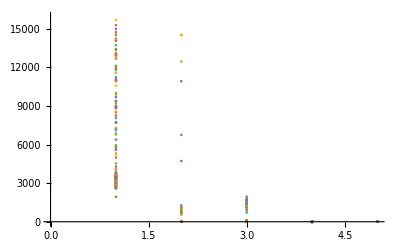

```mathematica
ListPlot[data]
```

This table shows the different star types from 1 to 5 and what temperature each star has. Looks like the most common star type is star type 1: Red Dwarf.

```mathematica
ListPointPlot3D[data]
```

-Graphics3D-

Looks like the bigger the star, the lower the tempature and lumosity becomes.

```mathematica
ListPlot3D[data]
```

-Graphics3D-

In deeper depth; looks like the higher the start type, the less tempature and luminosity. Looks like there is a couple of gaps around between 50, 100, 150, and 200 in terms of lumosity.